```mathematica
GeoStreamPlot[CloudGet["https://wolfr.am/CTZnxuQI"]]
```

-Graphics-

```mathematica
FacialFeatures[CloudGet["https://wolfr.am/CO20sk12"]]//Dataset
```

Dataset[<>]

```mathematica
NetMeasurements[NetModel["LeNet Trained on MNIST Data"], {-Graphics- -> 1, -Graphics- -> 9, -Graphics- -> 5, -Graphics- -> 2, -Graphics- -> 7}, "Perplexity"]
```

1.00039

```mathematica
Information[CloudPut[100!],"FileHashMD5"]
```

152401162714521721839695585034976020127

```mathematica
Information[CloudPut[100!]]
```

Cloud Object
065b8e30-a1b4-4b4b-ad9e-11f7266eaa96

```mathematica
CloudPut[100!]
```

CloudObject[https://www.wolframcloud.com/objects/b2106be5-8c9b-4cd3-99dc-ca9089696d3d]

```mathematica
CloudObjectInformation[CloudObject["https://www.wolframcloud.com/objects/b2106be5-8c9b-4cd3-99dc-ca9089696d3d"]]
```

CloudObject: b2106be5-8c9b-4cd3-99dc-ca9089696d3d

```mathematica
DateListLogPlot[Entity["Financial","NASDAQ:AAPL"][Dated["Price",All]]]
```

EntityValue::timeout: A network operation for EntityValue timed out. Please try again later.

EntityValue::nodat: Unable to download data. Some or all results may be missing.

DateListLogPlot::ldata: Missing[RetrievalFailure] is not a valid dataset or list of datasets.

DateListLogPlot[Missing[RetrievalFailure]]

```mathematica
ServiceConnect["BloombergTerminal"]
```

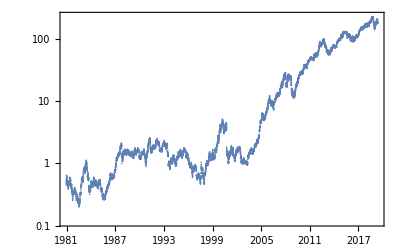

```mathematica
DateListLogPlot[
FinancialData["NASDAQ:AAPL", "Price", All], Joined->False]
```

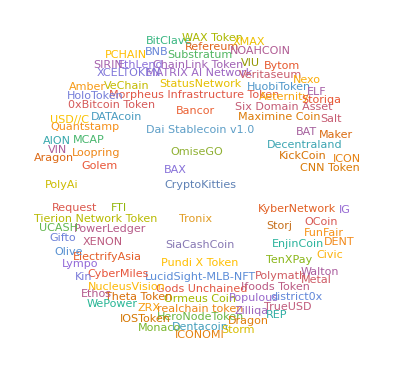

```mathematica
WordCloud[SortBy[BlockchainTokenData[All,{"Name","TransfersCount"}],Last]]
```

```mathematica
ServiceConnect["BloombergTerminal"]
```

ServiceConnect::unkn: The service BloombergTerminal is unknown, try providing authentication options.

ServiceConnect[BloombergTerminal]

```mathematica
heqn=D[u[x,t],t]==D[u[x,t],{x,2}];
```

```mathematica
ic=u[x,0]==E^(-x^2);
```

```mathematica
u[x,0]==ⅇ^(-x^2)
```

u[x,0]==ⅇ^(-x^2)

```mathematica
sol=DSolveValue[{heqn,ic},u[x,t],{x,t}]
```

(ⅇ^(-x^2/(1+4 t)))/(√(1+4 t))

```mathematica
Plot3D[sol,{t,-2.7074787643449203,2.7074787643449203},{x,-1.411408476546777,1.411408476546777}]
```

General::munfl: Exp[-1452.37] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1167.46] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1059.51] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics3D-

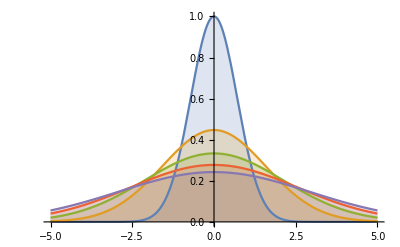

```mathematica
Plot[Evaluate[Table[sol,{t,0,4}]],{x,-5,5},PlotRange->All,Filling->Axis]
```

```mathematica
ic=u[x,0]==UnitBox[x]
sol=DSolveValue[{heqn,ic},u[x,t],{x,t}]
Plot3D[sol,{x,-2,2},{t,0,1},PlotRange->All,PlotPoints->250,Mesh->None]
```

u[x,0]==UnitBox[x]

1/2 (Erf[(1-2 x)/(4 √t)]+Erf[(1+2 x)/(4 √t)])

-Graphics3D-

```mathematica
∫_-5^5 (ⅇ^(-x^2/(1+4 t)))/(√(1+4 t))ⅆx
```

√π Erf[5/(√(1+4 t))]

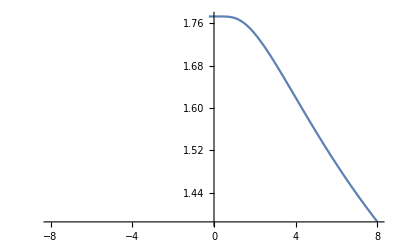

```mathematica
Plot[√π Erf[5/(√(1+4 t))],{t,-8,8}]
```

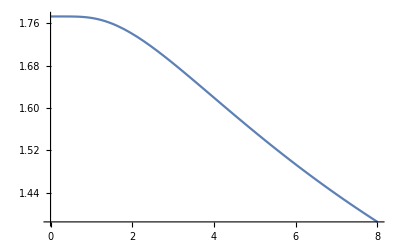

```mathematica
Plot[√π Erf[5/(√(1+4 t))],{t,0,8}]
```

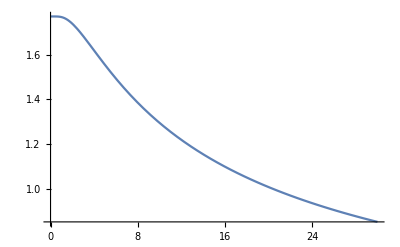

```mathematica
Plot[√π Erf[5/(√(1+4 t))],{t,0,30}]
```

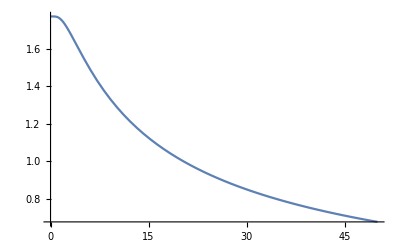

```mathematica
Plot[√π Erf[5/(√(1+4 t))],{t,0,50}]
```

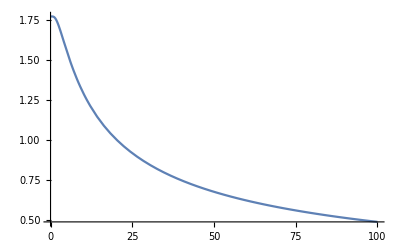

```mathematica
Plot[√π Erf[5/(√(1+4 t))],{t,0,100}]
```

```mathematica
Manipulate[
Plot[√π Erf[5/(√(1+4 t))],{t,0,a}],
{a, 1, 1000000, 1000}]
```

```mathematica
`
```

```mathematica
^((□_((_□^(√(_(□_(□^□)^□))))^□)^□)^□)
```

^((□_((_□^(√(_(□_(□^□)^□))))^□)^□)^□)

```mathematica
(*heqn=D[u[x,t],t]==D[u[x,t],{x,2}]; *)
```

```mathematica
D[U[x,t],t]==D[U[x,t], {x,2}]
```

U^(0,1)[x,t]==U^(2,0)[x,t]

```mathematica
DSolve[Derivative[0,1][U][x,t]==Derivative[2,0][U][x,t],{U[x,t],U[x,t]},{t,x}]
```

DSolve[U^(0,1)[x,t]==U^(2,0)[x,t],{U[x,t],U[x,t]},{t,x}]

```mathematica
1
```

1

```mathematica
D[f[x], x]
```

f'[x]

```mathematica
f
```

f

```mathematica
D[f[x], x]
```

f'[x]

```mathematica
∂^2/(∂_x)f[x]
```

```mathematica
∂/(∂x)
```

```mathematica
weqn=D[u[x,t],{t,2}]==D[u[x,t],{x,2}]
```

u^(0,2)[x,t]==u^(2,0)[x,t]

```mathematica
ic={u[x,0]==E^(-x^2),Derivative[0,1][u][x,0]==1}
```

{u[x,0]==ⅇ^(-x^2),u^(0,1)[x,0]==1}

```mathematica
DSolveValue[{weqn,ic},u[x,t],{x,t}]
```

1/2 (ⅇ^(-(-t+x)^2)+ⅇ^(-(t+x)^2))+t

```mathematica
Plot3D[1/2 (ⅇ^(-(-t+x)^2)+ⅇ^(-(t+x)^2))+t,{t,-1.2594732238832484,1.2594732238832484},{x,-1.2594732238832484,1.2594732238832484}]
```

-Graphics3D-

```mathematica
DSolveValue[{weqn,ic},u[x,t],{x,t}]
Plot3D[%,{x,-7,7},{t,0,4},Mesh->None]
```

1/2 (ⅇ^(-(-t+x)^2)+ⅇ^(-(t+x)^2))+t

-Graphics3D-

```mathematica
ic={u[x,0]==UnitBox[x]+UnitTriangle[x/3],Derivative[0,1][u][x,0]==0}
```

{u[x,0]==UnitBox[x]+UnitTriangle[x/3],u^(0,1)[x,0]==0}

```mathematica
DSolveValue[{weqn,ic},u[x,t],{x,t}]
```

1/2 (UnitBox[t-x]+UnitBox[t+x]+UnitTriangle[1/3 (-t+x)]+UnitTriangle[(t+x)/3])

```mathematica
DSolveValue[{weqn,ic},u[x,t],{x,t}];
Plot3D[%,{x,-7,7},{t,0,4},PlotRange->All,Mesh->None,ExclusionsStyle->Red]
```

-Graphics3D-

```mathematica
ic={u[x,0]==E^(-(x-6)^2)+E^(-(x+6)^2),Derivative[0,1][u][x,0]==1/2}
```

{u[x,0]==ⅇ^(-(-6+x)^2)+ⅇ^(-(6+x)^2),u^(0,1)[x,0]==1/2}

```mathematica
sol=DSolveValue[{weqn,ic},u[x,t],{x,t}]
```

1/2 (ⅇ^(-(-6-t+x)^2)+ⅇ^(-(6-t+x)^2)+ⅇ^(-(-6+t+x)^2)+ⅇ^(-(6+t+x)^2))+t/2

```mathematica
Plot3D[sol,{x,-30,30},{t,0,20},PlotRange->All,Mesh->None,PlotPoints->30]
```

General::munfl: Exp[-1295.9] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1295.8] is too small to represent as a normalized machine number; precision may be lost.

-Graphics3D-

```mathematica
Laplacian[f[x,y],{x,y}]
```

f^(0,2)[x,y]+f^(2,0)[x,y]

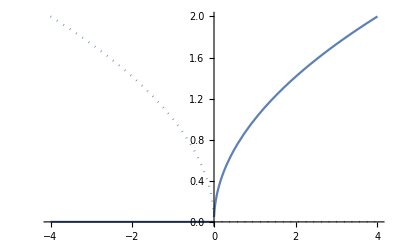

```mathematica
ReImPlot[√x,{x,-4,4}]
```

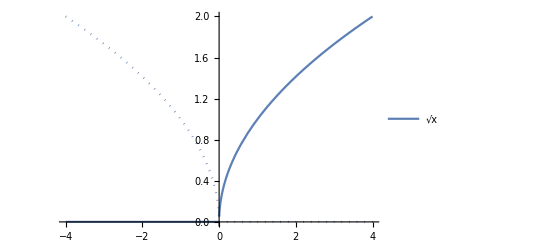

```mathematica
ReImPlot[√x,{x,-4,4}, PlotLegends->"Expressions"]
```

```mathematica
MultinormalDistribution[]
```

MultinormalDistribution::argrx: MultinormalDistribution called with 0 arguments; 2 arguments are expected.

MultinormalDistribution[]

```mathematica
MultinormalDistribution[μ, α]
```

MultinormalDistribution[μ,α]

```mathematica
PDF[MultinormalDistribution[μ, α],x]
```

MultinormalDistribution::vrprm: The value μ at position 1 in MultinormalDistribution[μ,α] is expected to be a list of real numbers.

PDF[MultinormalDistribution[μ,α],x]

```mathematica
PDF[NormalDistribution[],x]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
PDF[NormalDistribution[],x]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
leqn=Laplacian[u[x,y],{x,y}]==0
```

u^(0,2)[x,y]+u^(2,0)[x,y]==0

```mathematica
Ω=Rectangle[{0,0},{1,2}]
```

Rectangle[{0,0},{1,2}]

```mathematica
dcond=DirichletCondition[u[x,y]==Piecewise[{{UnitTriangle[2 x-1],y==0||y==2}},0],True]
```

DirichletCondition[u[x,y]==(Piecewise[{{UnitTriangle[1-2 x], y==0||y==2}, {0, True}}]),True]

```mathematica
sol=DSolveValue[{leqn,dcond},u[x,y],{x,y}∈Ω]//FullSimplify
```

(8 Cosh[π (-1+y) K[1]] Sech[π K[1]] Sin[1/2 π K[1]] Sin[π x K[1]])/(π^2 K[1]^2)K[1]1∞

```mathematica
asol=sol/.{∞->300}//Activate
```

(8 Cosh[π (-1+y)] Sech[π] Sin[π x])/π^2-(8 Cosh[3 π (-1+y)] Sech[3 π] Sin[3 π x])/(9 π^2)+(8 Cosh[5 π (-1+y)] Sech[5 π] Sin[5 π x])/(25 π^2)-(8 Cosh[7 π (-1+y)] Sech[7 π] Sin[7 π x])/(49 π^2)+(8 Cosh[9 π (-1+y)] Sech[9 π] Sin[9 π x])/(81 π^2)-(8 Cosh[11 π (-1+y)] Sech[11 π] Sin[11 π x])/(121 π^2)+(8 Cosh[13 π (-1+y)] Sech[13 π] Sin[13 π x])/(169 π^2)-(8 Cosh[15 π (-1+y)] Sech[15 π] Sin[15 π x])/(225 π^2)+(8 Cosh[17 π (-1+y)] Sech[17 π] Sin[17 π x])/(289 π^2)-(8 Cosh[19 π (-1+y)] Sech[19 π] Sin[19 π x])/(361 π^2)+(8 Cosh[21 π (-1+y)] Sech[21 π] Sin[21 π x])/(441 π^2)-(8 Cosh[23 π (-1+y)] Sech[23 π] Sin[23 π x])/(529 π^2)+(8 Cosh[25 π (-1+y)] Sech[25 π] Sin[25 π x])/(625 π^2)-(8 Cosh[27 π (-1+y)] Sech[27 π] Sin[27 π x])/(729 π^2)+(8 Cosh[29 π (-1+y)] Sech[29 π] Sin[29 π x])/(841 π^2)-(8 Cosh[31 π (-1+y)] Sech[31 π] Sin[31 π x])/(961 π^2)+(8 Cosh[33 π (-1+y)] Sech[33 π] Sin[33 π x])/(1089 π^2)-(8 Cosh[35 π (-1+y)] Sech[35 π] Sin[35 π x])/(1225 π^2)+(8 Cosh[37 π (-1+y)] Sech[37 π] Sin[37 π x])/(1369 π^2)-(8 Cosh[39 π (-1+y)] Sech[39 π] Sin[39 π x])/(1521 π^2)+(8 Cosh[41 π (-1+y)] Sech[41 π] Sin[41 π x])/(1681 π^2)-(8 Cosh[43 π (-1+y)] Sech[43 π] Sin[43 π x])/(1849 π^2)+(8 Cosh[45 π (-1+y)] Sech[45 π] Sin[45 π x])/(2025 π^2)-(8 Cosh[47 π (-1+y)] Sech[47 π] Sin[47 π x])/(2209 π^2)+(8 Cosh[49 π (-1+y)] Sech[49 π] Sin[49 π x])/(2401 π^2)-(8 Cosh[51 π (-1+y)] Sech[51 π] Sin[51 π x])/(2601 π^2)+(8 Cosh[53 π (-1+y)] Sech[53 π] Sin[53 π x])/(2809 π^2)-(8 Cosh[55 π (-1+y)] Sech[55 π] Sin[55 π x])/(3025 π^2)+(8 Cosh[57 π (-1+y)] Sech[57 π] Sin[57 π x])/(3249 π^2)-(8 Cosh[59 π (-1+y)] Sech[59 π] Sin[59 π x])/(3481 π^2)+(8 Cosh[61 π (-1+y)] Sech[61 π] Sin[61 π x])/(3721 π^2)-(8 Cosh[63 π (-1+y)] Sech[63 π] Sin[63 π x])/(3969 π^2)+(8 Cosh[65 π (-1+y)] Sech[65 π] Sin[65 π x])/(4225 π^2)-(8 Cosh[67 π (-1+y)] Sech[67 π] Sin[67 π x])/(4489 π^2)+(8 Cosh[69 π (-1+y)] Sech[69 π] Sin[69 π x])/(4761 π^2)-(8 Cosh[71 π (-1+y)] Sech[71 π] Sin[71 π x])/(5041 π^2)+(8 Cosh[73 π (-1+y)] Sech[73 π] Sin[73 π x])/(5329 π^2)-(8 Cosh[75 π (-1+y)] Sech[75 π] Sin[75 π x])/(5625 π^2)+(8 Cosh[77 π (-1+y)] Sech[77 π] Sin[77 π x])/(5929 π^2)-(8 Cosh[79 π (-1+y)] Sech[79 π] Sin[79 π x])/(6241 π^2)+(8 Cosh[81 π (-1+y)] Sech[81 π] Sin[81 π x])/(6561 π^2)-(8 Cosh[83 π (-1+y)] Sech[83 π] Sin[83 π x])/(6889 π^2)+(8 Cosh[85 π (-1+y)] Sech[85 π] Sin[85 π x])/(7225 π^2)-(8 Cosh[87 π (-1+y)] Sech[87 π] Sin[87 π x])/(7569 π^2)+(8 Cosh[89 π (-1+y)] Sech[89 π] Sin[89 π x])/(7921 π^2)-(8 Cosh[91 π (-1+y)] Sech[91 π] Sin[91 π x])/(8281 π^2)+(8 Cosh[93 π (-1+y)] Sech[93 π] Sin[93 π x])/(8649 π^2)-(8 Cosh[95 π (-1+y)] Sech[95 π] Sin[95 π x])/(9025 π^2)+(8 Cosh[97 π (-1+y)] Sech[97 π] Sin[97 π x])/(9409 π^2)-(8 Cosh[99 π (-1+y)] Sech[99 π] Sin[99 π x])/(9801 π^2)+(8 Cosh[101 π (-1+y)] Sech[101 π] Sin[101 π x])/(10201 π^2)-(8 Cosh[103 π (-1+y)] Sech[103 π] Sin[103 π x])/(10609 π^2)+(8 Cosh[105 π (-1+y)] Sech[105 π] Sin[105 π x])/(11025 π^2)-(8 Cosh[107 π (-1+y)] Sech[107 π] Sin[107 π x])/(11449 π^2)+(8 Cosh[109 π (-1+y)] Sech[109 π] Sin[109 π x])/(11881 π^2)-(8 Cosh[111 π (-1+y)] Sech[111 π] Sin[111 π x])/(12321 π^2)+(8 Cosh[113 π (-1+y)] Sech[113 π] Sin[113 π x])/(12769 π^2)-(8 Cosh[115 π (-1+y)] Sech[115 π] Sin[115 π x])/(13225 π^2)+(8 Cosh[117 π (-1+y)] Sech[117 π] Sin[117 π x])/(13689 π^2)-(8 Cosh[119 π (-1+y)] Sech[119 π] Sin[119 π x])/(14161 π^2)+(8 Cosh[121 π (-1+y)] Sech[121 π] Sin[121 π x])/(14641 π^2)-(8 Cosh[123 π (-1+y)] Sech[123 π] Sin[123 π x])/(15129 π^2)+(8 Cosh[125 π (-1+y)] Sech[125 π] Sin[125 π x])/(15625 π^2)-(8 Cosh[127 π (-1+y)] Sech[127 π] Sin[127 π x])/(16129 π^2)+(8 Cosh[129 π (-1+y)] Sech[129 π] Sin[129 π x])/(16641 π^2)-(8 Cosh[131 π (-1+y)] Sech[131 π] Sin[131 π x])/(17161 π^2)+(8 Cosh[133 π (-1+y)] Sech[133 π] Sin[133 π x])/(17689 π^2)-(8 Cosh[135 π (-1+y)] Sech[135 π] Sin[135 π x])/(18225 π^2)+(8 Cosh[137 π (-1+y)] Sech[137 π] Sin[137 π x])/(18769 π^2)-(8 Cosh[139 π (-1+y)] Sech[139 π] Sin[139 π x])/(19321 π^2)+(8 Cosh[141 π (-1+y)] Sech[141 π] Sin[141 π x])/(19881 π^2)-(8 Cosh[143 π (-1+y)] Sech[143 π] Sin[143 π x])/(20449 π^2)+(8 Cosh[145 π (-1+y)] Sech[145 π] Sin[145 π x])/(21025 π^2)-(8 Cosh[147 π (-1+y)] Sech[147 π] Sin[147 π x])/(21609 π^2)+(8 Cosh[149 π (-1+y)] Sech[149 π] Sin[149 π x])/(22201 π^2)-(8 Cosh[151 π (-1+y)] Sech[151 π] Sin[151 π x])/(22801 π^2)+(8 Cosh[153 π (-1+y)] Sech[153 π] Sin[153 π x])/(23409 π^2)-(8 Cosh[155 π (-1+y)] Sech[155 π] Sin[155 π x])/(24025 π^2)+(8 Cosh[157 π (-1+y)] Sech[157 π] Sin[157 π x])/(24649 π^2)-(8 Cosh[159 π (-1+y)] Sech[159 π] Sin[159 π x])/(25281 π^2)+(8 Cosh[161 π (-1+y)] Sech[161 π] Sin[161 π x])/(25921 π^2)-(8 Cosh[163 π (-1+y)] Sech[163 π] Sin[163 π x])/(26569 π^2)+(8 Cosh[165 π (-1+y)] Sech[165 π] Sin[165 π x])/(27225 π^2)-(8 Cosh[167 π (-1+y)] Sech[167 π] Sin[167 π x])/(27889 π^2)+(8 Cosh[169 π (-1+y)] Sech[169 π] Sin[169 π x])/(28561 π^2)-(8 Cosh[171 π (-1+y)] Sech[171 π] Sin[171 π x])/(29241 π^2)+(8 Cosh[173 π (-1+y)] Sech[173 π] Sin[173 π x])/(29929 π^2)-(8 Cosh[175 π (-1+y)] Sech[175 π] Sin[175 π x])/(30625 π^2)+(8 Cosh[177 π (-1+y)] Sech[177 π] Sin[177 π x])/(31329 π^2)-(8 Cosh[179 π (-1+y)] Sech[179 π] Sin[179 π x])/(32041 π^2)+(8 Cosh[181 π (-1+y)] Sech[181 π] Sin[181 π x])/(32761 π^2)-(8 Cosh[183 π (-1+y)] Sech[183 π] Sin[183 π x])/(33489 π^2)+(8 Cosh[185 π (-1+y)] Sech[185 π] Sin[185 π x])/(34225 π^2)-(8 Cosh[187 π (-1+y)] Sech[187 π] Sin[187 π x])/(34969 π^2)+(8 Cosh[189 π (-1+y)] Sech[189 π] Sin[189 π x])/(35721 π^2)-(8 Cosh[191 π (-1+y)] Sech[191 π] Sin[191 π x])/(36481 π^2)+(8 Cosh[193 π (-1+y)] Sech[193 π] Sin[193 π x])/(37249 π^2)-(8 Cosh[195 π (-1+y)] Sech[195 π] Sin[195 π x])/(38025 π^2)+(8 Cosh[197 π (-1+y)] Sech[197 π] Sin[197 π x])/(38809 π^2)-(8 Cosh[199 π (-1+y)] Sech[199 π] Sin[199 π x])/(39601 π^2)+(8 Cosh[201 π (-1+y)] Sech[201 π] Sin[201 π x])/(40401 π^2)-(8 Cosh[203 π (-1+y)] Sech[203 π] Sin[203 π x])/(41209 π^2)+(8 Cosh[205 π (-1+y)] Sech[205 π] Sin[205 π x])/(42025 π^2)-(8 Cosh[207 π (-1+y)] Sech[207 π] Sin[207 π x])/(42849 π^2)+(8 Cosh[209 π (-1+y)] Sech[209 π] Sin[209 π x])/(43681 π^2)-(8 Cosh[211 π (-1+y)] Sech[211 π] Sin[211 π x])/(44521 π^2)+(8 Cosh[213 π (-1+y)] Sech[213 π] Sin[213 π x])/(45369 π^2)-(8 Cosh[215 π (-1+y)] Sech[215 π] Sin[215 π x])/(46225 π^2)+(8 Cosh[217 π (-1+y)] Sech[217 π] Sin[217 π x])/(47089 π^2)-(8 Cosh[219 π (-1+y)] Sech[219 π] Sin[219 π x])/(47961 π^2)+(8 Cosh[221 π (-1+y)] Sech[221 π] Sin[221 π x])/(48841 π^2)-(8 Cosh[223 π (-1+y)] Sech[223 π] Sin[223 π x])/(49729 π^2)+(8 Cosh[225 π (-1+y)] Sech[225 π] Sin[225 π x])/(50625 π^2)-(8 Cosh[227 π (-1+y)] Sech[227 π] Sin[227 π x])/(51529 π^2)+(8 Cosh[229 π (-1+y)] Sech[229 π] Sin[229 π x])/(52441 π^2)-(8 Cosh[231 π (-1+y)] Sech[231 π] Sin[231 π x])/(53361 π^2)+(8 Cosh[233 π (-1+y)] Sech[233 π] Sin[233 π x])/(54289 π^2)-(8 Cosh[235 π (-1+y)] Sech[235 π] Sin[235 π x])/(55225 π^2)+(8 Cosh[237 π (-1+y)] Sech[237 π] Sin[237 π x])/(56169 π^2)-(8 Cosh[239 π (-1+y)] Sech[239 π] Sin[239 π x])/(57121 π^2)+(8 Cosh[241 π (-1+y)] Sech[241 π] Sin[241 π x])/(58081 π^2)-(8 Cosh[243 π (-1+y)] Sech[243 π] Sin[243 π x])/(59049 π^2)+(8 Cosh[245 π (-1+y)] Sech[245 π] Sin[245 π x])/(60025 π^2)-(8 Cosh[247 π (-1+y)] Sech[247 π] Sin[247 π x])/(61009 π^2)+(8 Cosh[249 π (-1+y)] Sech[249 π] Sin[249 π x])/(62001 π^2)-(8 Cosh[251 π (-1+y)] Sech[251 π] Sin[251 π x])/(63001 π^2)+(8 Cosh[253 π (-1+y)] Sech[253 π] Sin[253 π x])/(64009 π^2)-(8 Cosh[255 π (-1+y)] Sech[255 π] Sin[255 π x])/(65025 π^2)+(8 Cosh[257 π (-1+y)] Sech[257 π] Sin[257 π x])/(66049 π^2)-(8 Cosh[259 π (-1+y)] Sech[259 π] Sin[259 π x])/(67081 π^2)+(8 Cosh[261 π (-1+y)] Sech[261 π] Sin[261 π x])/(68121 π^2)-(8 Cosh[263 π (-1+y)] Sech[263 π] Sin[263 π x])/(69169 π^2)+(8 Cosh[265 π (-1+y)] Sech[265 π] Sin[265 π x])/(70225 π^2)-(8 Cosh[267 π (-1+y)] Sech[267 π] Sin[267 π x])/(71289 π^2)+(8 Cosh[269 π (-1+y)] Sech[269 π] Sin[269 π x])/(72361 π^2)-(8 Cosh[271 π (-1+y)] Sech[271 π] Sin[271 π x])/(73441 π^2)+(8 Cosh[273 π (-1+y)] Sech[273 π] Sin[273 π x])/(74529 π^2)-(8 Cosh[275 π (-1+y)] Sech[275 π] Sin[275 π x])/(75625 π^2)+(8 Cosh[277 π (-1+y)] Sech[277 π] Sin[277 π x])/(76729 π^2)-(8 Cosh[279 π (-1+y)] Sech[279 π] Sin[279 π x])/(77841 π^2)+(8 Cosh[281 π (-1+y)] Sech[281 π] Sin[281 π x])/(78961 π^2)-(8 Cosh[283 π (-1+y)] Sech[283 π] Sin[283 π x])/(80089 π^2)+(8 Cosh[285 π (-1+y)] Sech[285 π] Sin[285 π x])/(81225 π^2)-(8 Cosh[287 π (-1+y)] Sech[287 π] Sin[287 π x])/(82369 π^2)+(8 Cosh[289 π (-1+y)] Sech[289 π] Sin[289 π x])/(83521 π^2)-(8 Cosh[291 π (-1+y)] Sech[291 π] Sin[291 π x])/(84681 π^2)+(8 Cosh[293 π (-1+y)] Sech[293 π] Sin[293 π x])/(85849 π^2)-(8 Cosh[295 π (-1+y)] Sech[295 π] Sin[295 π x])/(87025 π^2)+(8 Cosh[297 π (-1+y)] Sech[297 π] Sin[297 π x])/(88209 π^2)-(8 Cosh[299 π (-1+y)] Sech[299 π] Sin[299 π x])/(89401 π^2)

```mathematica
Plot3D[asol//Evaluate,{x,y}∈Ω,PlotRange->All,PlotTheme->"Business"]
```

General::munfl: Sech[713.142] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Sech[719.425] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Sech[725.708] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics3D-

```mathematica
Sech[713.141532364883]
```

General::munfl: Sech[713.142] is too small to represent as a normalized machine number; precision may be lost.

3.86899×10^-310

```mathematica
heqn={Laplacian[u[x,y],{x,y}]+5 u[x,y]==0}
```

{5 u[x,y]+u^(0,2)[x,y]+u^(2,0)[x,y]==0}

```mathematica
UnitBox[x]
```

UnitBox[x]

```mathematica
D[UnitBox[x], x]
```

Piecewise[{{Indeterminate, x==1/2||x==-1/2}, {0, True}}]

```mathematica
Plot3D[√(x^2+y^2), {x,y}∈UnitBox[x]]
```

Plot3D::idomdim: {x,y}∈UnitBox[x] does not have a valid dimension as a plotting domain.

Plot3D[√(x^2+y^2),{x,y}∈UnitBox[x]]

```mathematica
Plot3D[√(x^2+y^2), {x,y}∈Disk[]]
```

-Graphics3D-

```mathematica
Manipulate[
Plot3D[(x^a+y^a)^(1/a), {x,y}∈Disk[]],
{a, 1, 10, 1}]
```

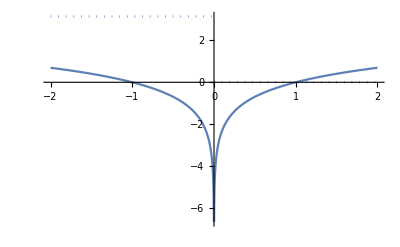

```mathematica
ReImPlot[Log[x], {x, -2, 2}]
```

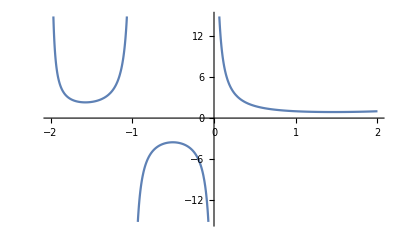

```mathematica
Plot[Gamma[z], {z, -2, 2}]
```

```mathematica
ComplexPlot[Gamma[z], {z, -2, 2}]
```

ComplexPlot::plld: Corners for z in {z,-2,2} must have distinct machine-precision real and imaginary parts.

ComplexPlot[Gamma[z],{z,-2,2}]

```mathematica
ComplexPlot[Gamma[z], {z, -2ⅈ, 2ⅈ}]
```

ComplexPlot::plld: Corners for z in {z,-2 ⅈ,2 ⅈ} must have distinct machine-precision real and imaginary parts.

ComplexPlot[Gamma[z],{z,-2 ⅈ,2 ⅈ}]

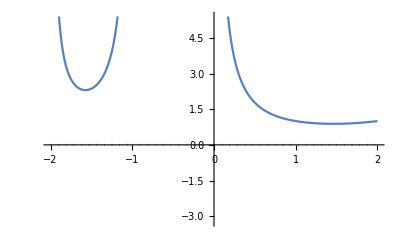

```mathematica
ReImPlot[Gamma[z], {z, -2, 2}]
```

```mathematica
Manipulate[DynamicModule[{ifun},ifun=NDSolveValue[{-Laplacian[u[x,y],{x,y}]==1,DirichletCondition[u[x,y]==0.,True]},u,{x,y}∈RegionDifference[Rectangle[{0,0},{1,1}],Rectangle[p1,p2]]];
ContourPlot[ifun[x,y],{x,y}∈ifun["ElementMesh"],ColorFunction->"TemperatureMap"]],{{p1,{0.3,0.2}},Locator},{{p2,{0.5,0.4}},Locator}]
```

```mathematica
eqn=I D[ψ[x,t],t]==D[ψ[x,t],{x,2}]
sol[x_,t_]=DSolveValue[{eqn,ψ[x,0]==Exp[-x^2]},ψ[x,t],{x,t}]
```

ⅈ ψ^(0,1)[x,t]==ψ^(2,0)[x,t]

Set::write: Tag Inactive in (8/π^2)[x_,t_] is Protected.

(ⅇ^(x^2/(-1+4 ⅈ t)))/(√2 √(1/2-2 ⅈ t))

```mathematica
Manipulate[Plot[Abs@sol[x,t],{x,-10,10},PlotRange->{0,1},PlotTheme->"Scientific",ImageSize->Medium],{t,0,5,Appearance->"Labeled"}]
```

```mathematica
Manipulate[Plot[Abs@sol[x,t],{x,-10,10},PlotRange->{0,1},PlotTheme->"Scientific",ImageSize->Medium],{t,0,5,Appearance->"Labeled"}]
```

```mathematica
eqn=I D[ψ[x,t],t]==D[ψ[x,t],{x,2}];
sol[x_,t_]=DSolveValue[{eqn,ψ[x,0]==Exp[-x^2]},ψ[x,t],{x,t}]
```

Set::write: Tag Inactive in (8/π^2)[x_,t_] is Protected.

(ⅇ^(x^2/(-1+4 ⅈ t)))/(√2 √(1/2-2 ⅈ t))

```mathematica
Clear[{eqn, sol}]
```

Clear::ssym: {eqn,sol} is not a symbol or a string.

```mathematica
Clear[eqn]
```

```mathematica
Clear[sol]
```

```mathematica
eqn=I D[ψ[x,t],t]==D[ψ[x,t],{x,2}]
sol[x_,t_]=DSolveValue[{eqn,ψ[x,0]==Exp[-x^2]},ψ[x,t],{x,t}]
```

ⅈ ψ^(0,1)[x,t]==ψ^(2,0)[x,t]

(ⅇ^(x^2/(-1+4 ⅈ t)))/(√2 √(1/2-2 ⅈ t))

```mathematica
Manipulate[Plot[Abs@sol[x,t],{x,-10,10},PlotRange->{0,1},PlotTheme->"Scientific",ImageSize->Medium],{t,0,5,Appearance->"Labeled"}]
```

```mathematica
eqn=I D[ψ[x,y,t],t]==-ℏ^2/(2 m)
Laplacian[ψ[x,y,t],{x,y}];
```

```mathematica
eqn=I D[ψ[x,y,t],t]==-ℏ^2/(2 m)
Laplacian[ψ[x,y,t],{x,y}]
```

ⅈ ψ^(0,0,1)[x,y,t]==-ℏ^2/(2 m)

ψ^(0,2,0)[x,y,t]+ψ^(2,0,0)[x,y,t]

```mathematica
bcs={ψ[0,y,t]==0,ψ[xMax,y,t]==0,ψ[x,yMax,t]==0,ψ[x,0,t]==0};
```

```mathematica
DSolveValue[{eqn,bcs},ψ[x,y,t],{x,y,t}]
```

DSolveValue[{ⅈ ψ^(0,0,1)[x,y,t]==-ℏ^2/(2 m),{ψ[0,y,t]==0,ψ[xMax,y,t]==0,ψ[x,yMax,t]==0,ψ[x,0,t]==0}},ψ[x,y,t],{x,y,t}]

```mathematica
initEigen=ψ[x,y,0]==2/Sqrt[xMax yMax] Sin[(π x)/xMax] Sin[(π y)/yMax]
```

ψ[x,y,0]==(2 Sin[(π x)/xMax] Sin[(π y)/yMax])/(√(xMax yMax))

```mathematica
DSolveValue[{eqn,bcs,initEigen},ψ[x,y,t],{x,y,t}]
```

DSolveValue[{ⅈ ψ^(0,0,1)[x,y,t]==-ℏ^2/(2 m),{ψ[0,y,t]==0,ψ[xMax,y,t]==0,ψ[x,yMax,t]==0,ψ[x,0,t]==0},ψ[x,y,0]==(2 Sin[(π x)/xMax] Sin[(π y)/yMax])/(√(xMax yMax))},ψ[x,y,t],{x,y,t}]

```mathematica
initSum=ψ[x,y,0]==Sqrt[2]/Sqrt[xMax yMax] (Sin[(2 π x)/xMax] Sin[(π y)/yMax]+Sin[(π x)/xMax] Sin[(3 π y)/yMax])
```

ψ[x,y,0]==(√2 (Sin[(2 π x)/xMax] Sin[(π y)/yMax]+Sin[(π x)/xMax] Sin[(3 π y)/yMax]))/(√(xMax yMax))

```mathematica
sol=DSolveValue[{eqn,bcs,initSum},ψ[x,y,t],{x,y,t}]
```

DSolveValue[{ⅈ ψ^(0,0,1)[x,y,t]==-ℏ^2/(2 m),{ψ[0,y,t]==0,ψ[xMax,y,t]==0,ψ[x,yMax,t]==0,ψ[x,0,t]==0},ψ[x,y,0]==(√2 (Sin[(2 π x)/xMax] Sin[(π y)/yMax]+Sin[(π x)/xMax] Sin[(3 π y)/yMax]))/(√(xMax yMax))},ψ[x,y,t],{x,y,t}]

```mathematica
ℏ=QuantityMagnitude[Quantity[1.,"ReducedPlanckConstant"],"ElectronMass"*("Nanometers")^2/"Femtoseconds"]
```

0.115768

```mathematica
ρ[x_,y_,t_]=FullSimplify[ComplexExpand[Conjugate[sol] sol]]/.{m->1,xMax->1,yMax->1}
```

DSolveValue[{ⅈ ψ^(0,0,1)[x,y,t]==-0.00670107,{ψ[0,y,t]==0,ψ[1,y,t]==0,ψ[x,1,t]==0,ψ[x,0,t]==0},ψ[x,y,0]==√2 (Sin[2 π x] Sin[π y]+Sin[π x] Sin[3 π y])},ψ[x,y,t],{x,y,t}]^2

```mathematica
ListAnimate[Table[Plot3D[ρ[x,y,t],{x,0,1},{y,0,1},PlotTheme->{"Scientific","SolidGrid"},AxesLabel->{"\!\(\*
StyleBox[\"x\", \"SO\"]\) (nm)"," \!\(\*
StyleBox[\"y\", \"SO\"]\) (nm)","\!\(\*
StyleBox[\"ρ\", \"SO\"]\) (\!\(\*SuperscriptBox[\(nm\), \(-2\)]\))"},ImageSize->Medium,PlotRange->{0,7}],{t,0,19,.5}]]
```

DSolve::dupv: Duplicate variable 0.0000715 found in DSolve[{ⅈ ψ^(0,0,1)[0.0000715,0.0000715,0.]==-0.00670107,{«1»},ψ[0.0000715,0.0000715,0]==3.56777×10^-7},{ψ},«1»].

DSolve::twoivarg: The function ψ[0.0000715,0.0000715,0.] has two independent variables in one argument. The independent variables should be in separate arguments.

DSolve::ivar2: The independent variable 0.0000715 should not appear in two different arguments of the dependent variable ψ[0.0000715,0.0000715,0.].

NDSolveValue::dsvar: 0.0000715 cannot be used as a variable.

First::nofirst: {} has zero length and no first element.

NDSolveValue::dsvar: 0.0715001 cannot be used as a variable.

General::stop: Further output of NDSolveValue::dsvar will be suppressed during this calculation.

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

DSolve::dupv: Duplicate variable 0.0715001 found in DSolve[«1»].

DSolve::twoivarg: The function ψ[0.0715001,0.0715001,0.] has two independent variables in one argument. The independent variables should be in separate arguments.

DSolve::ivar2: The independent variable 0.0715001 should not appear in two different arguments of the dependent variable ψ[0.0715001,0.0715001,0.].

DSolve::dupv: Duplicate variable 0.142929 found in DSolve[«1»].

General::stop: Further output of DSolve::dupv will be suppressed during this calculation.

DSolve::twoivarg: The function ψ[0.142929,0.142929,0.] has two independent variables in one argument. The independent variables should be in separate arguments.

General::stop: Further output of DSolve::twoivarg will be suppressed during this calculation.

DSolve::ivar2: The independent variable 0.142929 should not appear in two different arguments of the dependent variable ψ[0.142929,0.142929,0.].

General::stop: Further output of DSolve::ivar2 will be suppressed during this calculation.